### Find and illustrate a Hamiltonian Win Cycle (HWC)

#### Data

Test data: 
English Premier League 2023-24
Cut off at the earliest date with HWC

Format: csv, with first 7 columns: 
{year,month,day,home_team,away_team,home_goals,away_goals}

```mathematica
(* path to input csv *)
scoreCSVpath=FileNameJoin[{NotebookDirectory[],"input","eng-tier-1-2023-2024.csv"}];
FileExistsQ@scoreCSVpath
```

True

Discard draws

```mathematica
scoreData=Import[scoreCSVpath];
useData=Select[scoreData,#[[6]]!=#[[7]]&];
Dimensions@%
```

{87,7}

```mathematica
Grid[useData,Dividers->All,Alignment->Left]
```

2023 | 8 | 11 | Burnley | Manchester City | 0 | 3
2023 | 8 | 12 | Arsenal | Nottingham | 2 | 1
2023 | 8 | 12 | Brighton | Luton | 4 | 1
2023 | 8 | 12 | Everton | Fulham | 0 | 1
2023 | 8 | 12 | Newcastle | Aston Villa | 5 | 1
2023 | 8 | 12 | Sheffield United | Crystal Palace | 0 | 1
2023 | 8 | 14 | Manchester United | Wolverhampton | 1 | 0
2023 | 8 | 18 | Nottingham | Sheffield United | 2 | 1
2023 | 8 | 19 | Fulham | Brentford | 0 | 3
2023 | 8 | 19 | Liverpool | Bournemouth | 3 | 1
2023 | 8 | 19 | Manchester City | Newcastle | 1 | 0
2023 | 8 | 19 | Tottenham | Manchester United | 2 | 0
2023 | 8 | 19 | Wolverhampton | Brighton | 1 | 4
2023 | 8 | 20 | Aston Villa | Everton | 4 | 0
2023 | 8 | 20 | West Ham | Chelsea | 3 | 1
2023 | 8 | 21 | Crystal Palace | Arsenal | 0 | 1
2023 | 8 | 25 | Chelsea | Luton | 3 | 0
2023 | 8 | 26 | Bournemouth | Tottenham | 0 | 2
2023 | 8 | 26 | Brighton | West Ham | 1 | 3
2023 | 8 | 26 | Everton | Wolverhampton | 0 | 1
2023 | 8 | 26 | Manchester United | Nottingham | 3 | 2
2023 | 8 | 27 | Burnley | Aston Villa | 1 | 3
2023 | 8 | 27 | Newcastle | Liverpool | 1 | 2
2023 | 8 | 27 | Sheffield United | Manchester City | 1 | 2
2023 | 9 | 1 | Luton | West Ham | 1 | 2
2023 | 9 | 2 | Brighton | Newcastle | 3 | 1
2023 | 9 | 2 | Burnley | Tottenham | 2 | 5
2023 | 9 | 2 | Chelsea | Nottingham | 0 | 1
2023 | 9 | 2 | Manchester City | Fulham | 5 | 1
2023 | 9 | 3 | Arsenal | Manchester United | 3 | 1
2023 | 9 | 3 | Crystal Palace | Wolverhampton | 3 | 2
2023 | 9 | 3 | Liverpool | Aston Villa | 3 | 0
2023 | 9 | 16 | Aston Villa | Crystal Palace | 3 | 1
2023 | 9 | 16 | Fulham | Luton | 1 | 0
2023 | 9 | 16 | Manchester United | Brighton | 1 | 3
2023 | 9 | 16 | Newcastle | Brentford | 1 | 0
2023 | 9 | 16 | Tottenham | Sheffield United | 2 | 1
2023 | 9 | 16 | West Ham | Manchester City | 1 | 3
2023 | 9 | 16 | Wolverhampton | Liverpool | 1 | 3
2023 | 9 | 17 | Everton | Arsenal | 0 | 1
2023 | 9 | 23 | Brentford | Everton | 1 | 3
2023 | 9 | 23 | Burnley | Manchester United | 0 | 1
2023 | 9 | 23 | Manchester City | Nottingham | 2 | 0
2023 | 9 | 24 | Brighton | Bournemouth | 3 | 1
2023 | 9 | 24 | Chelsea | Aston Villa | 0 | 1
2023 | 9 | 24 | Liverpool | West Ham | 3 | 1
2023 | 9 | 24 | Sheffield United | Newcastle | 0 | 8
2023 | 9 | 30 | Bournemouth | Arsenal | 0 | 4
2023 | 9 | 30 | Aston Villa | Brighton | 6 | 1
2023 | 9 | 30 | Everton | Luton | 1 | 2
2023 | 9 | 30 | Manchester United | Crystal Palace | 0 | 1
2023 | 9 | 30 | Newcastle | Burnley | 2 | 0
2023 | 9 | 30 | Tottenham | Liverpool | 2 | 1
2023 | 9 | 30 | West Ham | Sheffield United | 2 | 0
2023 | 9 | 30 | Wolverhampton | Manchester City | 2 | 1
2023 | 10 | 2 | Fulham | Chelsea | 0 | 2
2023 | 10 | 3 | Luton | Burnley | 1 | 2
2023 | 10 | 7 | Burnley | Chelsea | 1 | 4
2023 | 10 | 7 | Everton | Bournemouth | 3 | 0
2023 | 10 | 7 | Fulham | Sheffield United | 3 | 1
2023 | 10 | 7 | Luton | Tottenham | 0 | 1
2023 | 10 | 7 | Manchester United | Brentford | 2 | 1
2023 | 10 | 8 | Arsenal | Manchester City | 1 | 0
2023 | 10 | 21 | Bournemouth | Wolverhampton | 1 | 2
2023 | 10 | 21 | Brentford | Burnley | 3 | 0
2023 | 10 | 21 | Liverpool | Everton | 2 | 0
2023 | 10 | 21 | Manchester City | Brighton | 2 | 1
2023 | 10 | 21 | Newcastle | Crystal Palace | 4 | 0
2023 | 10 | 21 | Sheffield United | Manchester United | 1 | 2
2023 | 10 | 22 | Aston Villa | West Ham | 4 | 1
2023 | 10 | 23 | Tottenham | Fulham | 2 | 0
2023 | 10 | 27 | Crystal Palace | Tottenham | 1 | 2
2023 | 10 | 28 | Bournemouth | Burnley | 2 | 1
2023 | 10 | 28 | Arsenal | Sheffield United | 5 | 0
2023 | 10 | 28 | Chelsea | Brentford | 0 | 2
2023 | 10 | 29 | Aston Villa | Luton | 3 | 1
2023 | 10 | 29 | Liverpool | Nottingham | 3 | 0
2023 | 10 | 29 | Manchester United | Manchester City | 0 | 3
2023 | 10 | 29 | West Ham | Everton | 0 | 1
2023 | 11 | 4 | Brentford | West Ham | 3 | 2
2023 | 11 | 4 | Burnley | Crystal Palace | 0 | 2
2023 | 11 | 4 | Fulham | Manchester United | 0 | 1
2023 | 11 | 4 | Manchester City | Bournemouth | 6 | 1
2023 | 11 | 4 | Newcastle | Arsenal | 1 | 0
2023 | 11 | 4 | Sheffield United | Wolverhampton | 2 | 1
2023 | 11 | 5 | Nottingham | Aston Villa | 2 | 0
2023 | 11 | 6 | Tottenham | Chelsea | 1 | 4

#### Find HWC

```mathematica
(* helper *)
winEdge=Which[#[[6]]>#[[7]],#[[4]]->#[[5]],#[[6]]<#[[7]],#[[5]]->#[[4]],True,{}]&;
(* make directed winner->loser graph *)
winEdgeList=winEdge/@useData;
Length@%
```

87

Select an arbitrary HWC. This fails if there are none. If there are any, there are usually many!

```mathematica
hwcEdgeList=FindHamiltonianCycle[winEdgeList][[1]]
```

{Manchester City->Newcastle,Newcastle->Arsenal,Arsenal->Crystal Palace,Crystal Palace->Manchester United,Manchester United->Nottingham,Nottingham->Aston Villa,Aston Villa->Chelsea,Chelsea->Tottenham,Tottenham->Liverpool,Liverpool->West Ham,West Ham->Brighton,Brighton->Bournemouth,Bournemouth->Burnley,Burnley->Luton,Luton->Everton,Everton->Brentford,Brentford->Fulham,Fulham->Sheffield United,Sheffield United->Wolverhampton,Wolverhampton->Manchester City}

#### Graph

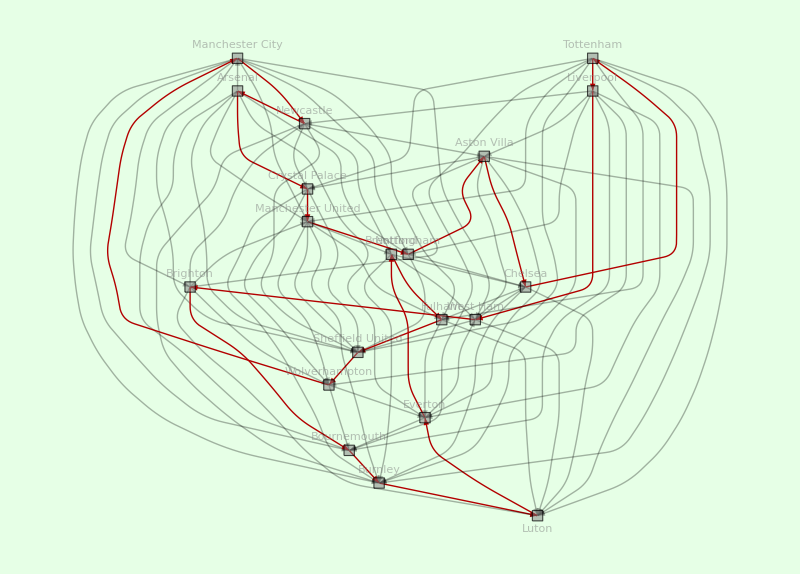

```mathematica
winGraph0=Graph[winEdgeList,
VertexLabels->"Name",VertexShapeFunction->"Square",VertexSize->.7,VertexStyle->Opacity[.5,Gray],
EdgeStyle->Opacity[.3,Black],EdgeShapeFunction->{{Arrowheads[Medium],Arrow[#,.02]}&},
GraphLayout->"LayeredDigraphEmbedding",
AspectRatio->.7,
ImagePadding->20,
ImageSize->800];

winGraph=Graph[winGraph0,
GraphHighlight->hwcEdgeList,GraphHighlightStyle->"Thick",
Background->Lighter[Green,.9]]
```

#### Text

List score data for matches that are part of the HWC.
Start the list from the latest winner

```mathematica
hwcPosList=Flatten[FirstPosition[winEdgeList,#]&/@hwcEdgeList];winDates=useData[[hwcPosList]]ᵀ[[{1,2,3}]]ᵀ;
{cutPos}=1-FirstPosition[winDates,Sort[winDates][[-1]]];
```

Short text version:

```mathematica
winnersList=RotateRight[First/@winEdgeList[[hwcPosList]],cutPos];
winCycleString=StringRiffle[Join[winnersList,{winnersList[[1]]}]," > "]
StringLength@winCycleString
```

Chelsea > Tottenham > Liverpool > West Ham > Brighton > Bournemouth > Burnley > Luton > Everton > Brentford > Fulham > Sheffield United > Wolverhampton > Manchester City > Newcastle > Arsenal > Crystal Palace > Manchester United > Nottingham > Aston Villa > Chelsea

265

Longer text version

```mathematica
hwcScoreData=useData[[RotateRight[hwcPosList,cutPos]]];
hwScoreDates=DateString[#[[{1,2,3}]],{"Day"," ","MonthNameShort"}]&/@hwcScoreData;
hwScoreTab=If[#[[6]]>#[[7]],Join[#[[4;;7]],{"(H)"}],Join[#[[{5,4,7,6}]],{"(A)"}]]&/@hwcScoreData;
hwScoreStrings=StringRiffle[{#[[1]],"beat",#[[2]],ToString@#[[3]]<>"-"<>ToString@#[[4]],#[[5]]}]&/@hwScoreTab;

Grid[{hwScoreDates,hwScoreStrings}ᵀ,Alignment->Left,Spacings->1]
```

06 Nov | Chelsea beat Tottenham 4-1 (A)
30 Sep | Tottenham beat Liverpool 2-1 (H)
24 Sep | Liverpool beat West Ham 3-1 (H)
26 Aug | West Ham beat Brighton 3-1 (A)
24 Sep | Brighton beat Bournemouth 3-1 (H)
28 Oct | Bournemouth beat Burnley 2-1 (H)
03 Oct | Burnley beat Luton 2-1 (A)
30 Sep | Luton beat Everton 2-1 (A)
23 Sep | Everton beat Brentford 3-1 (A)
19 Aug | Brentford beat Fulham 3-0 (A)
07 Oct | Fulham beat Sheffield United 3-1 (H)
04 Nov | Sheffield United beat Wolverhampton 2-1 (H)
30 Sep | Wolverhampton beat Manchester City 2-1 (H)
19 Aug | Manchester City beat Newcastle 1-0 (H)
04 Nov | Newcastle beat Arsenal 1-0 (H)
21 Aug | Arsenal beat Crystal Palace 1-0 (A)
30 Sep | Crystal Palace beat Manchester United 1-0 (A)
26 Aug | Manchester United beat Nottingham 3-2 (H)
05 Nov | Nottingham beat Aston Villa 2-0 (H)
24 Sep | Aston Villa beat Chelsea 1-0 (A)

#### Export output

```mathematica
outputDir=FileNameJoin[{NotebookDirectory[],"output"}]
```

```mathematica
Export[FileNameJoin[{outputDir,FileBaseName[scoreCSVpath]<>".svg"}],winGraph]
Export[FileNameJoin[{outputDir,FileBaseName[scoreCSVpath]<>".txt"}],winCycleString]
Export[FileNameJoin[{outputDir,FileBaseName[scoreCSVpath]<>".csv"}],hwcScoreData]
```

#### Etc

How many HWCs are there?

```mathematica
Length@FindHamiltonianCycle[winEdgeList,10^7]
```

25